```mathematica
(* set directory for image exports *)
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

/Users/gracezhang/Documents/GitHub/Oral_Exam_Paper

Nonlinear system with a stable hyperbolic equilibrium.

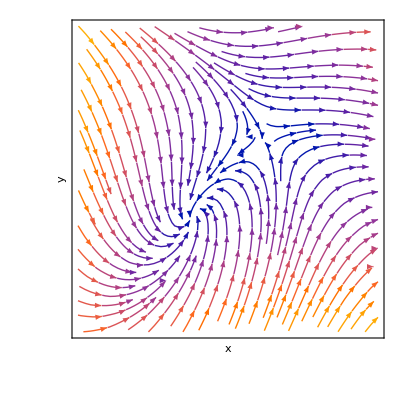

```mathematica
plot1 = Show[StreamPlot[{x+y+x^2+y^2,x-y-x^2+y^2},{x,-2.5,1.5},{y,-2.5,1.5},AxesLabel->{x,y} , FrameTicks->None, Background->RGBColor[1,1,1, 0.5]]]
```

Linearization at the stable fixed point (x,y) = (-1,-1):

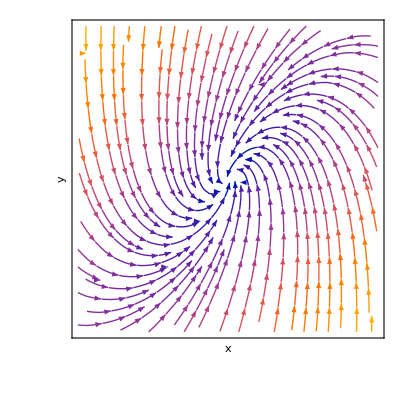

```mathematica
plot2 = Show[StreamPlot[{-x-y, 3x-3y},{x,-2,2},{y,-2,2},AxesLabel->{x,y} , FrameTicks->None, Background->RGBColor[1,1,1, 0.5]]]
```

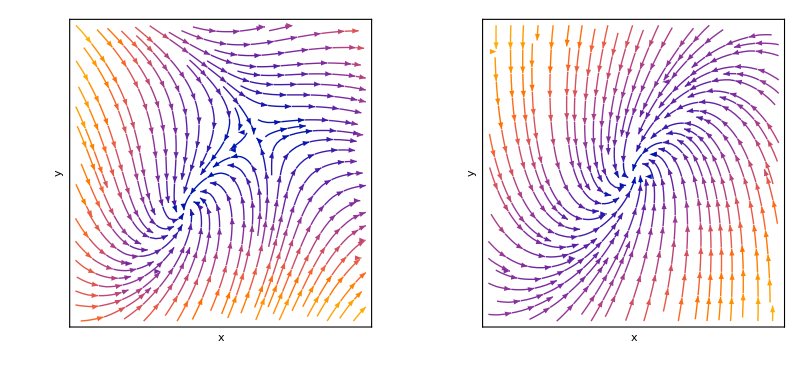

figs/linearization_of_nonlinear_stable_point.png

```mathematica
image= GraphicsRow[{plot1, plot2}]
Export["figs/linearization_of_nonlinear_stable_point.png", image, Background->None]
```

```mathematica
Eigenvalues[{{-1,-1},{3,-3}}]
```

{-2+ⅈ √2,-2-ⅈ √2}